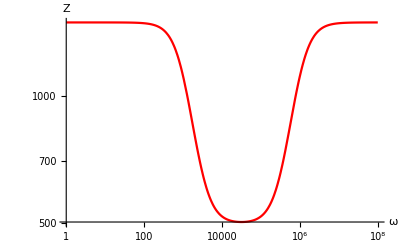

```mathematica
(*-Graphics-*)
ClearAll["Global`*"]
soucastky = {
r1 -> 1 *10^3,
r2 -> 1 *10^3,
r3 -> 1 *10^3,
r4 -> 1 *10^3,
l1 -> 1 *10^-3,
c1 -> 1 *10^-6
};
konverze = {
(* moznost prekonverzace na zx -> rx a nasledne pouzivani zx misto rx *)
zl -> ⅉ*ω*l1,
zc -> 1/(ⅉ*ω*c1)
};

Z= (r1*zl)/(r1+zl)+(r2*zc)/(r2+zc)+(r3*r4)/(r3+r4);
vys = Z/.konverze /.soucastky;
LogLogPlot[Abs[vys],{ω,1,10^8}, AxesLabel->{"ω", "Z"},PlotStyle->  Red]
```